# Attack Transient softener

## Release and attack filters

```mathematica
releaseOnlySVF[X_,fc_,sr_]:=Module[{Q,prevY,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,k,attackMode,output},
Q=0.5;
output =X;
g = Tan[π fc /sr];
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = 0;
attackMode = True;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY, 

(* attack mode: follow input exactly *)
attackMode = True;
output[[i]] = X[[i]],

(* release mode: set gradient to zero and start from last value *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False;ic1=0; ic2=prevY];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
];

prevY= output[[i]];
];

output
]


attackOnlySVF[X_,fc_,sr_]:=Module[{Q,prevY,prevY2,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,gInv,k,attackMode,output},
Q=0.5;
output =X;
g = Tan[π fc /sr];
gInv = 1.0/g;
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = prevY2 =0;
attackMode = False;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY, 

(* attack mode: filter *)
(* if this is the first sample of the attack, switch to attack mode *)
If[!attackMode,
attackMode = True; ic1 = 0.5*(prevY-prevY2)*gInv; ic2 = prevY;
];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
,

(* release mode: copy input to output *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False];
output[[i]] = X[[i]];
];

prevY2 = prevY;
prevY= output[[i]];
];

output
]


attackOnlySVF2[X_,fc_,sr_]:=Module[{Q,prevY,prevY2,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,gInv,k,attackMode,output},
Q=0.5;
output =X;
g = Tan[π fc /sr];
gInv = 1.0/g;
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = prevY2 =0;
attackMode = False;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY, 

(* attack mode: filter *)
(* if this is the first sample of the attack, switch to attack mode *)
If[!attackMode,
attackMode = True; ic1 = 0.5*(prevY-prevY2)*gInv; ic2 = prevY;
];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
,

(* release mode: copy input to output *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False];
output[[i]] = X[[i]];
];

prevY2 = prevY;
prevY= output[[i]];
];

output
]


lowpassSVF[X_,fc_,sr_]:=Module[{Q,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,k,output},
Q=0.5;
output =X;
g = Tan[π fc /sr];
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
];

output
]
```

## Attack Softener functions

```mathematica
takeNegative[X_]:=(X -Abs[X])/2
upperLimit[X_,limit_]:=takeNegative[X-limit]+limit

attackSoftener[X_,sampleRate_]:=Module[{b1, b2,b3,b4, attackFc, releaseFc},
(* set attack time and release time *)
attackFc = 10;
releaseFc = 10;

(* generate volume envelope *)
b1 = Abs[X];
b1 = releaseOnlySVF[b1,releaseFc,sampleRate];
b2 = lowpassSVF[b1,attackFc,sampleRate]; 

(* find the ratio that X has to be reduced in order to force it beneath the envelope *)
b3 = b2 / (Abs[X]+ 0.0001);
b3 = upperLimit[b3,1];

(* filter the control signal to reduce aliasing *)
b4 = releaseOnlySVF[b3,releaseFc,sampleRate];
b4 = lowpassSVF[b4,attackFc,sampleRate];

(* force X to fit beneath the envelope *)
(* X * b4 *)
{X,b2,b4,X*b4}
]
```

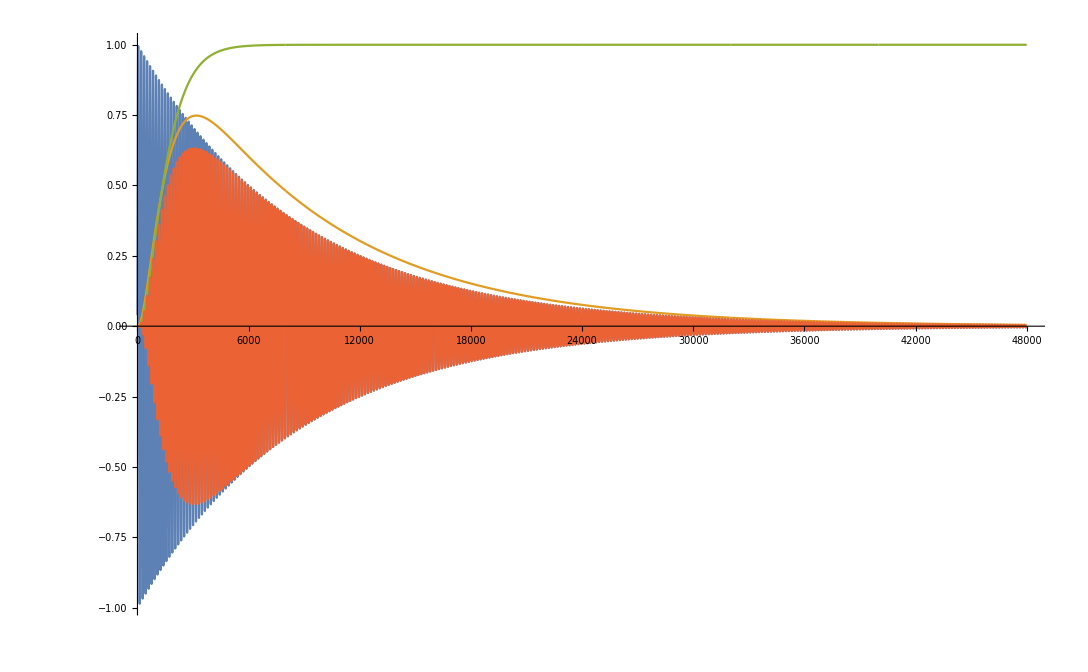

```mathematica
sampleRate = 48000;
freq = 300;
testInput = Table[2^(-8t/sampleRate)Sin[freq 2 π N[t]/sampleRate],{t,1,sampleRate}];
testOutput = attackSoftener[testInput,sampleRate];
ListLinePlot[testOutput]
```

```mathematica
(* convert to a sound *)
audioObject1 = Sound[ListPlay[testInput,SampleRate->48000]]
audioObject2 = Sound[ListPlay[testOutput,SampleRate->48000]]

(* save to audio file *)
Export["~/Desktop/test1.wav",audioObject1,AudioEncoding->"Integer24"]
Export["~/Desktop/test2.wav",audioObject2,AudioEncoding->"Integer24"]
```

-Graphics-

-Graphics-

~/Desktop/test1.wav

~/Desktop/test2.wav